# PDE Test Problems Van Der Vorst

@article{doi:10.1137/0913035,
author = {van der Vorst, H. A.},
title = {Bi-CGSTAB: A Fast and Smoothly Converging Variant of Bi-CG for the Solution of Nonsymmetric Linear Systems},
journal = {SIAM Journal on Scientific and Statistical Computing},
volume = {13},
number = {2},
pages = {631-644},
year = {1992},
doi = {10.1137/0913035},
URL = {    https://doi.org/10.1137/0913035
},
eprint = {   https://doi.org/10.1137/0913035},
abstract = { Recently the Conjugate Gradients-Squared (CG-S) method has been proposed as an attractive variant of the Bi-Conjugate Gradients (Bi-CG) method. However, it has been observed that CG-S may lead to a rather irregular convergence behaviour, so that in some cases rounding errors can even result in severe cancellation effects in the solution. In this paper, another variant of Bi-CG is proposed which does not seem to suffer from these negative effects. Numerical experiments indicate also that the new variant, named Bi-CGSTAB, is often much more efficient than CG-S. }
}

## Test 1: Δu=f on Ω=[0,1]^2 Dirichlet BC 150×150 grid

The fully interior points i=2:n-1 use the standard five point stencil.  The boundary adjacent points

```mathematica
n=150;
Δx=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A1=SparseArray[{},{m,m}];
Do[
k=ijTok[n][i,j];
A1⟦k,k⟧=4.0;
If[1≤i+1≤n,A1⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A1⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A1⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A1⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,1,n}]
A1
```

SparseArray[…]

## Code: B-BCG Eq:1-4

```mathematica
BlockBiCGStep[A_,M_][{{R_,P_},{Rb_,Pb_}}]:= Module[
{m,b,
AP,AtPb,PbtAP,PbtAPInv,
MR,MtRb,RbtMR,RbtMRInv,
RNew,PNew,RbNew,PbNew,α,αb,β,βb,γ,γb},
{m,b}=Dimensions[P];
(* Conditioning matrices set to Identity *)
γ=γb=IdentityMatrix[b];
(* Precompute products A *)
{AP,AtPb}={A.P,Aᵀ.Pb};
 PbtAP=Pbᵀ.AP;
 PbtAPInv=Inverse[PbtAP];
(* Precompute products M *)
{MR,MtRb}={M.R,Mᵀ.Rb};
RbtMR = Rbᵀ.MR;
RbtMRInv = Inverse[RbtMR];
(* Compute αs 3.x and βs 4.x *)
{α,αb}={PbtAPInv.γbᵀ.RbtMR, PbtAPInv.γᵀ.RbtMRᵀ};
{β,βb}={PbtAPInv.γbᵀ.RbtMR, PbtAPInv.γᵀ.RbtMRᵀ};
Print[MatrixForm[Map[
SingularValueList[#,Tolerance->0]&,{α,αb,β,βb}]
]];
(* Updates 1.x and 2.x *)
(* Returning updated {{R,P},{Rb,Pb}} *)
{
{R-A.P.α,(M.R+P.β).γ},
{Rb-Aᵀ.Pb.αb,(Mᵀ.Rb+Pb.βb).γb}
}
]
```

Testing.

```mathematica
{m,b}={15,3};
A=RandomReal[{-1,1},{m,m}];
(* Perfect preconditioning ϵ=0 *)
ϵ=0.1;
M=Inverse[A]+ϵ RandomReal[{-1,1},{m,m}];
{R,Rb}=RandomReal[{-1,1},{2,m,b}];
{P,Pb}={M.R,Mᵀ.Rb};
```

```mathematica
Data=Nest[BlockBiCGStep[A,M],{{R,P},{Rb,Pb}},6];
```

(1.42658 | 1.05111 | 0.872894
20.9661 | 0.980071 | 0.0636982
1.42658 | 1.05111 | 0.872894
20.9661 | 0.980071 | 0.0636982)

(0.0637389 | 0.0309346 | 0.000201645
3.59995 | 0.0105104 | 0.0000105081
0.0637389 | 0.0309346 | 0.000201645
3.59995 | 0.0105104 | 0.0000105081)

(49.5457 | 0.703467 | 0.000581124
824.374 | 0.226325 | 0.000108558
49.5457 | 0.703467 | 0.000581124
824.374 | 0.226325 | 0.000108558)

(77.0081 | 0.00815416 | 0.00158898
761332. | 0.00208759 | 6.27802×10^-7
77.0081 | 0.00815416 | 0.00158898
761332. | 0.00208759 | 6.27802×10^-7)

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.99636×10^7,-4.02764×10^6,5.29157×10^7},{-3.4538×10^7,«22»,-«22»},{1.15154×10^7,-1.16055×10^6,1.52475×10^7}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.40379×10^9,-6.41534×10^8,8.57036×10^9},{-5.53438×10^9,«21»,-«20»},{1.84523×10^9,-1.84856×10^8,2.46952×10^9}} may contain significant numerical errors.

(13394.1 | 1.48905 | 0.0000857038
4.36197×10^11 | 0.0281637 | 0.0000833667
13394.1 | 1.48905 | 0.0000857038
4.36197×10^11 | 0.0281637 | 0.0000833667)

Inverse::luc: Result for Inverse of badly conditioned matrix {{5.25608×10^15,-5.5584×10^14,7.31071×10^15},{-4.54249×10^15,«21»,-«22»},{1.51452×10^15,-1.60163×10^14,2.10655×10^15}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

(5.10555×10^6 | 3.8799 | 0.00450242
1.45388×10^16 | 0.659889 | 0.108607
5.10555×10^6 | 3.8799 | 0.00450242
1.45388×10^16 | 0.659889 | 0.108607)

## Intro: P.A≈I

Suppose we have an n×n sparse matrix A then we can find the sparse matrix P (with a specified sparsity pattern) that minimizes 
	||P.A-I(||)_F^2.
Specifically if 𝒫 is a sparsity pattern class then 
	argmin_(P∈𝒫)||P.A-I(||)_F^2
can be computed relatively efficiently.  The minimum is well defined because the cost function is a positive definite sum of squares in the non-zero entries of P. The minimizer is unique unless the sum of squares is degenerate!

Note, if A is invertible and we consider dense matrices the minimum zero is attained when P=A^-1.

## Parallel Algorithm

Of course, the product P.A is computed by running along the rows of P and down the columns of A.  So each row of P.A depends only on the corresponding row of P. Splitting the cost function up by row shows that each row of P is determined by minimizing the reduced cost function
	 argmin_(P⟦i,:⟧∈𝒫_i)||P⟦i,:⟧.A-e_i(||)_^2.
In other words, each row of P is determined by a substantially smaller least squares problem defined by the product of a sparse vector and the sparse matrix A.

If row i of P has nz_i allowed non-zeros then the LS problem for row i is n×nz_i.  The problems for each row are completely independent!  They require no communication.  Such a problem is called embarrassingly parallel.

### Small Scale Demo

Suppose my matrix is

```mathematica
A=({{2.0, 0, 0, 1.2}, {1.2, 4.0, 0, 0}, {0, 0, 3.1, 0.1}, {0, 0.1, 0, 0.6}});
```

I can assume that my P has the same sparsity pattern as A in other words.

```mathematica
P=({{p11, 0, 0, p14}, {p21, p22, 0, 0}, {0, 0, p33, p34}, {0, p42, 0, p44}});
Id=IdentityMatrix[4];
```

Then the 4 partial objective functions are

```mathematica
Table[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
Simplify[temp.temp],
{i,1,4}]
```

{1.+5.44 p11^2+0.37 p14^2+p11 (-4.+1.44 p14),1.+5.44 p21^2-8. p22+4.8 p21 p22+17.44 p22^2,1.+9.62 p33^2+p33 (-6.2+0.12 p34)+0.37 p34^2,1.+17.44 p42^2-1.2 p44+0.8 p42 p44+0.37 p44^2}

The minimizer of each is easily computed by setting the derivatives equal to zero.

```mathematica
ParallelTable[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
quad=temp.temp;
Minimize[quad,Variables[quad]],
{i,1,4}]
```

{{0.00963597,{p11→0.495182,p14→-0.963597}},{0.0232692,{p21→-0.107728,p22→0.244183}},{0.0000281231,{p33→0.322572,p34→-0.0523089}},{0.00228833,{p42→-0.0381388,p44→1.66285}}}

Of course, for a small problem there is no need to split the sum up like this and you can perform the “big” minimization on the sum.

```mathematica
quad=Sum[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
temp.temp,
{i,1,4}];
{val,sub}=Minimize[quad,Variables[quad]]
```

{0.0352216,{p11→0.495182,p14→-0.963597,p21→-0.107728,p22→0.244183,p33→0.322572,p34→-0.0523089,p42→-0.0381388,p44→1.66285}}

Whichever way you do it you get something that you might hope was a decent preconditioner.  Of course the way to check how good a preconditioner it is to check the spectrum of P.A

```mathematica
PStar=P/.sub;
Eigenvalues[PStar.A]
SingularValueList[PStar.A]
```

{1.00923+0.105776 ⅈ,1.00923-0.105776 ⅈ,0.999972+0. ⅈ,0.946351+0. ⅈ}

{1.0525,1.00057,0.998797,0.926438}

### Larger Scale Computation

For a larger sparse matrix there will be lots of structural zeros in 
	P.A
which do not need to be computed or summed.  Efficient algorithms avoid this unnecessary work using a variety of tricks.   Here is an attempt at avoiding some of this work in a simple way on a familiar matrix.

```mathematica
n=10;
m=n^2;
A=SparseArray[{},{m,m}];
ijTok[i_,j_,n_]:=i+(j-1)*n;
Do[
k=ijTok[i,j,n];
A⟦k,k⟧=4;
If[1≤i+1≤n,A⟦k,ijTok[i+1,j,n]⟧=-1.0];
If[1≤i-1≤n,A⟦k,ijTok[i-1,j,n]⟧=-1.0];
If[1≤j+1≤n,A⟦k,ijTok[i,j+1,n]⟧=-1.0];
If[1≤j-1≤n,A⟦k,ijTok[i,j-1,n]⟧=-1.0],
{i,1,n},{j,1,n}]
ListPlot[Eigenvalues[A]];
```

We need to choose a sparsity pattern.  I am going to use the sparsity pattern of A and not bother to split it up by row.

```mathematica
ARules=ArrayRules[A];
nz=Length[ARules]-1;
PRules=Table[ARules⟦i,1⟧->p[i],{i,nz}];
P=SparseArray[PRules,{m,m}];
quad=Total[Flatten[P.A-IdentityMatrix[m]]^2];
{val,sub}=Minimize[quad,Variables[quad]];
P=SparseArray[PRules/.sub,{m,m}];
TabView[{
"A"->MatrixPlot[A,PlotLegends->Automatic],
"A^-1"->MatrixPlot[Inverse[Normal[A]],PlotLegends->Automatic],
"P"->MatrixPlot[P,PlotLegends->Automatic],
"P.A-Id"->MatrixPlot[P.A-IdentityMatrix[m],PlotLegends->Automatic],
"λ_A"->ListPlot[ReIm[Eigenvalues[A]],PlotRange->All],
"λ_(P . A)"->ListPlot[ReIm[Eigenvalues[P.A]],PlotRange->All]
}
]
```

12345

The preconditioner does not need to to be symmetric!

```mathematica
Map[Norm[#,"Frobenius"]&,{A-Aᵀ,P-Pᵀ,P.A-IdentityMatrix[m],A.P-IdentityMatrix[m],A}]
```

{0.,0.0249786,2.58686,2.58919,44.2719}

This “symbolic” computation can be computed efficiently by splitting by row or by columns and avoiding the symbols p_i.

You can do any sparsity pattern you want!

```mathematica
ASqRules=ArrayRules[A.A];
nz=Length[ASqRules]-1;
PRules=Table[ASqRules⟦i,1⟧->p[i],{i,nz}];
P=SparseArray[PRules,{m,m}];
quad=Total[Flatten[P.A-IdentityMatrix[m]]^2];
{val,sub}=Minimize[quad,Variables[quad]];
P=SparseArray[PRules/.sub,{m,m}];
TabView[{
"A"->MatrixPlot[A,PlotLegends->Automatic],
"A^-1"->MatrixPlot[Inverse[Normal[A]],PlotLegends->Automatic],
"P"->MatrixPlot[P,PlotLegends->Automatic],
"P.A-Id"->MatrixPlot[P.A-IdentityMatrix[m],PlotLegends->Automatic],
"λ_A"->ListPlot[ReIm[Eigenvalues[A]],PlotRange->All],
"λ_(P . A)"->ListPlot[ReIm[Eigenvalues[P.A]],PlotRange->All]
}
]
```

123456

Adding non-zeros to the sparsity pattern ensures that the residual has reduced.

```mathematica
Map[Norm[#,"Frobenius"]&,{A-Aᵀ,P-Pᵀ,P.A-IdentityMatrix[m],A.P-IdentityMatrix[m],A}]
```

{0.,0.14502,1.75177,1.80736,44.2719}

There are techniques to add non-zeros recursively.  The block-like structure in the inverse comes from the “warp-around” numbering scheme for the PDE. It suggests block techniques might be useful.  So blocking techniques were developed.

### Comparison With Sparse ILU

I am going to compute a Sparse Cholesky

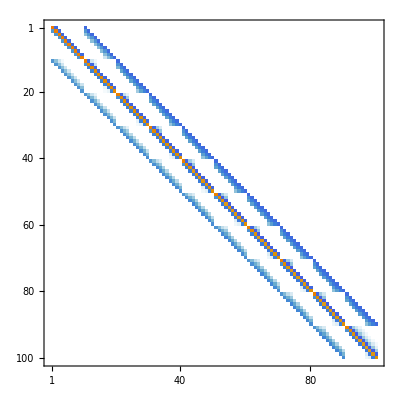

```mathematica
n=10;
m=n^2;
A=SparseArray[{},{m,m}];
ijTok[i_,j_,n_]:=i+(j-1)*n;
Do[
k=ijTok[i,j,n];
A⟦k,k⟧=4;
If[1≤i+1≤n,A⟦k,ijTok[i+1,j,n]⟧=-1.0];
If[1≤i-1≤n,A⟦k,ijTok[i-1,j,n]⟧=-1.0];
If[1≤j+1≤n,A⟦k,ijTok[i,j+1,n]⟧=-1.0];
If[1≤j-1≤n,A⟦k,ijTok[i,j-1,n]⟧=-1.0],
{i,1,n},{j,1,n}]
LU=SparseArray`SparseMatrixILU[A]⟦1⟧;
MatrixPlot[LU]
```